```mathematica
<<MultivariateStatistics`
```

```mathematica
detailIDdr={{AL, AK, AZ, AR, CA, CO, CT, DC, DE,FL,GA,HI,ID,IL,IN,IA,KS,KY,LA,ME,MD,MA,MI,MN,MS,MO,MT,NE,NV,NH,NJ,NM,NY,NC,ND,OH,OK,OR,PA,RI,SC,SD,TN,TX,UT,VT,VA,WA,WV,WI,WY},{416468,416471,416484,416491,416498,416505,416508,416623,416511,417861,416514,416520,416523,416532,416542,416545,416554,416557,416560,416569,416584,416593,416599,416602,416612,416619,416487,416490,416496,416502,416516,416526,416529,416534,416539,416548,416551,416590,416595,416605,416608,416611,416617,416632,416636,416639,416642,416645,416648,416653,416654},
{416469,416472,416485,416493,416500,416506,416509,416624,416512,417866,416515,416521,416524,416537,416543,416546,416555,416558,416561,416570,416585,416594,416600,416603,416614,416621,416488,416492,416497,416503,416518,416527,416530,416535,416540,416549,416552,416591,416597,416606,416609,416613,416618,416634,416637,416640,416643,416646,416649,416651,416655}};
```

```mathematica
ev=Import["http://www.electoral-vote.com/evp2008/Pres/Excel/today.csv"];
```

```mathematica
datad=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[2,i]] ]],1],{i,51}];
```

```mathematica
datar=Table[Drop[Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId="<>ToString[detailIDdr[[3,i]] ]],1],{i,51}];
```

```mathematica
datad[[5,664,2;;-1]]=datad[[5,663,2;;-1]](*data error: CA price on 9.11=3 instead of 91.2*)
```

{91.2,91.2,91.2,91.2,0}

```mathematica
datar[[23,657,2;;-1]]=datar[[23,656,2;;-1]]
```

{38.5,36.2,40,39.9,35}

```mathematica
history=Table[,{2},{120}];
```

```mathematica
closed=datad[[All,All,5]];
closer=datar[[All,All,5]];
window=90;window1=window+1;
```

```mathematica
For[h=1,h≤120,h++,
daysago=h+4;

returnsd=Table[Log[closed[[i,j-1]]/closed[[i,j]]],{i,51},{j,-window-daysago,-1-daysago}];
returnsr=Table[Log[closer[[a,b-1]]/closer[[a,b]]],{a,51},{b,-window-daysago,-1-daysago}];
cvard=Table[,{51},{51}];cvarr=Table[,{51},{51}];
For[d=1,d≤51,d++,
For[c=1, c≤51, c++, cvard[[d,c]]=Covariance[returnsd[[c]],returnsd[[d]] ];
cvarr[[d,c]]=Covariance[returnsr[[c]],returnsr[[d]] ]
]];
timeleft=DateDifference[DateList[][[1;;3]],{2008,11,4}]+daysago;
closed2=Table[closed[[e,-window-daysago;;-1-daysago]],{e,51}];
closer2=Table[closer[[f,-window-daysago;;-1-daysago]],{f,51}];
nowd=closed2[[All,-1]];nowr=closer2[[All,-1]];
simsdet=Table[
ds=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvard+.000001],timeleft]]];
rs=Exp[Transpose[RandomReal[MultinormalDistribution[Table[0,{51}],cvarr+.000001],timeleft]]];
endd=nowd*Times@@@ds;
endr=nowr*Times@@@rs;
chanced=endd/(endd+endr);

Table[t=chanced[[y]];v=ev[[2;;-2,2]][[y]];Which[t<.3,0,.3<t<.7,If[RandomReal[]<t,v,0],t>.7,v],{y,51}],{200}
];
sims=Map[Total,simsdet];
history[[1,h]]=Count[sims,n_/;n>268]/Length[sims]//N;
history[[2,h]]=Mean[sims]//N;
Print[h]
]
```

1

2

3

4

5

6

7

8

9

10

11

12

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

41

42

43

44

45

46

47

48

49

50

51

52

53

54

55

56

57

58

59

60

61

62

63

64

65

66

67

68

69

70

71

72

73

74

75

76

77

78

79

80

81

82

83

84

85

86

87

88

89

90

91

92

93

94

95

96

97

98

99

100

101

102

103

104

105

106

107

108

109

110

111

112

113

114

115

116

117

118

119

120

```mathematica
DatePlus[{2008,11,3},-120]
```

{2008,7,6}

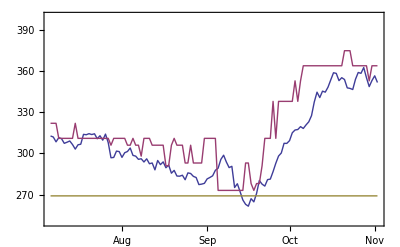

```mathematica
DateListPlot[{Reverse[Take[history[[2]],120]],Reverse[Take[winning,120]],Table[269,{120}]},{2008,7,6},Joined->True,PlotRange->{Automatic,{250,400}},PlotStyle->Thick]
```

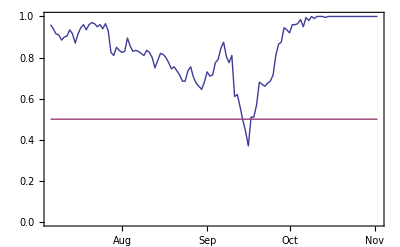

```mathematica
DateListPlot[{Reverse[Take[history[[1]],120]],Table[.5,{120}]},{2008,7,6},Joined->True,PlotRange->{Automatic,{0,1}},PlotStyle->Thick]
```

```mathematica
natr=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=376101"];
natd=Import["http://data.intrade.com/graphing/jsp/downloadClosingPrice.jsp?contractId=409933"];
```

```mathematica
chancend=Take[natd[[All,5]],-300]/(Take[natd[[All,5]],-300]+Take[natr[[All,5]],-300]);
```

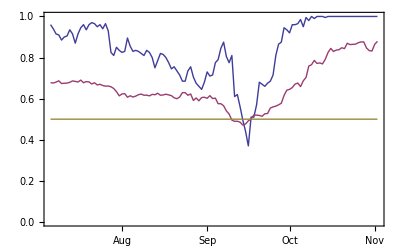

```mathematica
DateListPlot[{Reverse[history[[1]]],chancend[[-123;;-4]],Table[.5,{120}]},{2008,7,6},Joined->True,PlotRange->{Automatic,{0,1}},PlotStyle->Thick]
```